```mathematica
FullSimplify[Expand[FullSimplify[2/(1-eta)^2*Integrate[(eta*x-1)Cos[Q*D*x],{x,0,1}]]]]
```

(2 (eta (-1+Cos[D Q])+D (-1+eta) Q Sin[D Q]))/(D^2 (-1+eta)^2 Q^2)

```mathematica
Factor[(2(D (-1+eta) Q Sin[D Q]))/(D^2 (-1+eta)^2 Q^2)]
```

(2 Sin[D Q])/(D (-1+eta) Q)

```mathematica
FullSimplify[(2 (eta (-1+Cos[D Q])))/(D^2 (-1+eta)^2 Q^2)]
```

(2 eta (-1+Cos[D Q]))/(D^2 (-1+eta)^2 Q^2)

```mathematica
FullSimplify[Expand[FullSimplify[2/(1-eta)^2*Integrate[(eta*0-1)Cos[Q*D*x],{x,0,1}]]]]
```

-(2 Sin[D Q])/(D (-1+eta)^2 Q)

```mathematica
FullSimplify[Expand[FullSimplify[2/(1-eta)^2*Integrate[(eta*x-0)Cos[Q*D*x],{x,0,1}]]]]
```

(2 eta (-1+Cos[D Q]+D Q Sin[D Q]))/(D^2 (-1+eta)^2 Q^2)

```mathematica
S1D[eta_,Q_,D_]:=1/(1-eta*((2 (eta (-1+Cos[D Q])+D (-1+eta) Q Sin[D Q]))/(D^2 (-1+eta)^2 Q^2)))
```

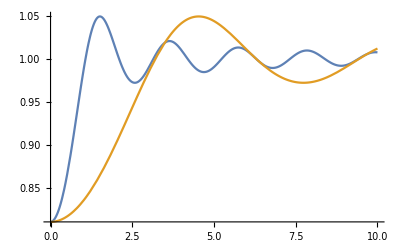

```mathematica
Plot[{S1D[0.1,Q,3],S1D[0.1,Q,1]},{Q,0,10},PlotRange->All]
```